```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])- t22(hop[a[3],a[6]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->1.5,cj->U/5,U->4,t23->x t22,t22->0.3}
```

{Δ→1.5,𝒿→U/5,U→4,t23→t22 x,t22→0.3}

```mathematica
{Δ->1.5,𝒿->U/5,U->4,t23->t22 x,t22->0.3}
```

{Δ→1.5,𝒿→U/5,U→4,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

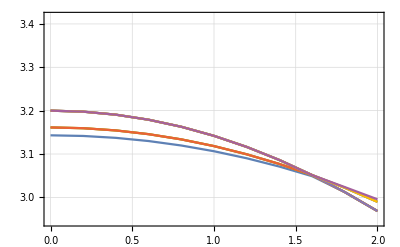

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

4.76184×10^-7

1

0.0000705899

1

0.000280937

1

0.000631536

1

0.00112241

1

0.0017536

1

0.00252512

1

0.00343702

1

0.00448929

1

0.00568193

1

0.00701489

1

0.00848808

1

0.0101013

1

0.0118544

1

0.0137471

1

0.0157788

1

0.0179491

1

5.87441

1

5.85902

1

5.84278

1

5.82571

2

2.

2

1.99992

2

1.99967

2

1.99926

2

1.99869

2

1.99796

2

1.99706

2

1.99599

2

1.99477

2

1.99338

2

1.99182

2

1.9901

2

1.98821

2

1.98616

2

1.98395

2

1.98157

2

1.97903

2

5.87441

2

5.85902

2

5.84278

2

5.82571

3

2.

3

1.99992

3

1.99967

3

1.99926

3

1.99869

3

1.99796

3

1.99706

3

1.99599

3

1.99477

3

1.99338

3

1.99182

3

1.9901

3

1.98821

3

1.98616

3

1.98395

3

1.98157

3

1.97903

3

5.87441

3

5.85902

3

5.84278

3

5.82571

4

2.

4

1.99992

4

1.99967

4

1.99926

4

1.99869

4

1.99796

4

1.99706

4

1.99599

4

1.99477

4

1.99338

4

1.99182

4

1.9901

4

1.98821

4

1.98616

4

1.98395

4

1.98157

4

1.97903

4

5.87441

4

5.85902

4

5.84278

4

5.82571

5

6.

5

5.99958

5

5.99831

5

5.9962

5

5.99324

5

5.98942

5

5.98474

5

5.97918

5

5.97275

5

5.96543

5

5.95721

5

5.94809

5

5.93807

5

5.92714

5

5.9153

5

5.90256

5

5.88893

5

5.87441

5

5.85902

5

5.84278

5

5.82571

6

6.

6

5.99958

6

5.99831

6

5.9962

6

5.99324

6

5.98942

6

5.98474

6

5.97918

6

5.97275

6

5.96543

6

5.95721

6

5.94809

6

5.93807

6

5.92714

6

5.9153

6

5.90256

6

5.88893

6

0.0202573

6

1.97346

6

1.97044

6

1.96725

7

6.

7

5.99958

7

5.99831

7

5.9962

7

5.99324

7

5.98942

7

5.98474

7

5.97918

7

5.97275

7

5.96543

7

5.95721

7

5.94809

7

5.93807

7

5.92714

7

5.9153

7

5.90256

7

5.88893

7

1.97633

7

1.97346

7

1.97044

7

1.96725

8

6.

8

5.99958

8

5.99831

8

5.9962

8

5.99324

8

5.98942

8

5.98474

8

5.97918

8

5.97275

8

5.96543

8

5.95721

8

5.94809

8

5.93807

8

5.92714

8

5.9153

8

5.90256

8

5.88893

8

1.97633

8

1.97346

8

1.97044

8

1.96725

9

6.

9

5.99958

9

5.99831

9

5.9962

9

5.99324

9

5.98942

9

5.98474

9

5.97918

9

5.97275

9

5.96543

9

5.95721

9

5.94809

9

5.93807

9

5.92714

9

5.9153

9

5.90256

9

5.88893

9

1.97633

9

0.0227025

9

0.0252837

9

0.0279997

10

1.99999

10

1.99994

10

1.99979

10

1.99955

10

1.99921

10

1.99878

10

1.99826

10

1.99767

10

1.99702

10

1.9963

10

1.99554

10

1.99474

10

1.99391

10

1.99309

10

1.99227

10

1.99148

10

1.99073

10

1.99005

10

1.98944

10

1.98893

10

1.98851

```mathematica
data1//MatrixForm
```

(1 | 0. | 4.76184×10^-7 | 3.14312
1 | 0.1 | 0.0000705899 | 3.14275
1 | 0.2 | 0.000280937 | 3.14165
1 | 0.3 | 0.000631536 | 3.13982
1 | 0.4 | 0.00112241 | 3.13725
1 | 0.5 | 0.0017536 | 3.13395
1 | 0.6 | 0.00252512 | 3.12992
1 | 0.7 | 0.00343702 | 3.12515
1 | 0.8 | 0.00448929 | 3.11964
1 | 0.9 | 0.00568193 | 3.11339
1 | 1. | 0.00701489 | 3.1064
1 | 1.1 | 0.00848808 | 3.09868
1 | 1.2 | 0.0101013 | 3.09021
1 | 1.3 | 0.0118544 | 3.081
1 | 1.4 | 0.0137471 | 3.07105
1 | 1.5 | 0.0157788 | 3.06034
1 | 1.6 | 0.0179491 | 3.04889
1 | 1.7 | 5.87441 | 3.03238
1 | 1.8 | 5.85902 | 3.01217
1 | 1.9 | 5.84278 | 2.99084
1 | 2. | 5.82571 | 2.9684
2 | 0. | 2. | 3.16126
2 | 0.1 | 1.99992 | 3.16083
2 | 0.2 | 1.99967 | 3.15954
2 | 0.3 | 1.99926 | 3.15739
2 | 0.4 | 1.99869 | 3.15438
2 | 0.5 | 1.99796 | 3.15051
2 | 0.6 | 1.99706 | 3.14578
2 | 0.7 | 1.99599 | 3.14019
2 | 0.8 | 1.99477 | 3.13374
2 | 0.9 | 1.99338 | 3.12643
2 | 1. | 1.99182 | 3.11826
2 | 1.1 | 1.9901 | 3.10924
2 | 1.2 | 1.98821 | 3.09936
2 | 1.3 | 1.98616 | 3.08863
2 | 1.4 | 1.98395 | 3.07704
2 | 1.5 | 1.98157 | 3.0646
2 | 1.6 | 1.97903 | 3.05131
2 | 1.7 | 5.87441 | 3.03238
2 | 1.8 | 5.85902 | 3.01217
2 | 1.9 | 5.84278 | 2.99084
2 | 2. | 5.82571 | 2.9684
3 | 0. | 2. | 3.16126
3 | 0.1 | 1.99992 | 3.16083
3 | 0.2 | 1.99967 | 3.15954
3 | 0.3 | 1.99926 | 3.15739
3 | 0.4 | 1.99869 | 3.15438
3 | 0.5 | 1.99796 | 3.15051
3 | 0.6 | 1.99706 | 3.14578
3 | 0.7 | 1.99599 | 3.14019
3 | 0.8 | 1.99477 | 3.13374
3 | 0.9 | 1.99338 | 3.12643
3 | 1. | 1.99182 | 3.11826
3 | 1.1 | 1.9901 | 3.10924
3 | 1.2 | 1.98821 | 3.09936
3 | 1.3 | 1.98616 | 3.08863
3 | 1.4 | 1.98395 | 3.07704
3 | 1.5 | 1.98157 | 3.0646
3 | 1.6 | 1.97903 | 3.05131
3 | 1.7 | 5.87441 | 3.03238
3 | 1.8 | 5.85902 | 3.01217
3 | 1.9 | 5.84278 | 2.99084
3 | 2. | 5.82571 | 2.9684
4 | 0. | 2. | 3.16126
4 | 0.1 | 1.99992 | 3.16083
4 | 0.2 | 1.99967 | 3.15954
4 | 0.3 | 1.99926 | 3.15739
4 | 0.4 | 1.99869 | 3.15438
4 | 0.5 | 1.99796 | 3.15051
4 | 0.6 | 1.99706 | 3.14578
4 | 0.7 | 1.99599 | 3.14019
4 | 0.8 | 1.99477 | 3.13374
4 | 0.9 | 1.99338 | 3.12643
4 | 1. | 1.99182 | 3.11826
4 | 1.1 | 1.9901 | 3.10924
4 | 1.2 | 1.98821 | 3.09936
4 | 1.3 | 1.98616 | 3.08863
4 | 1.4 | 1.98395 | 3.07704
4 | 1.5 | 1.98157 | 3.0646
4 | 1.6 | 1.97903 | 3.05131
4 | 1.7 | 5.87441 | 3.03238
4 | 1.8 | 5.85902 | 3.01217
4 | 1.9 | 5.84278 | 2.99084
4 | 2. | 5.82571 | 2.9684
5 | 0. | 6. | 3.2
5 | 0.1 | 5.99958 | 3.19942
5 | 0.2 | 5.99831 | 3.19768
5 | 0.3 | 5.9962 | 3.19477
5 | 0.4 | 5.99324 | 3.19071
5 | 0.5 | 5.98942 | 3.18548
5 | 0.6 | 5.98474 | 3.17909
5 | 0.7 | 5.97918 | 3.17154
5 | 0.8 | 5.97275 | 3.16283
5 | 0.9 | 5.96543 | 3.15296
5 | 1. | 5.95721 | 3.14192
5 | 1.1 | 5.94809 | 3.12973
5 | 1.2 | 5.93807 | 3.11638
5 | 1.3 | 5.92714 | 3.10187
5 | 1.4 | 5.9153 | 3.08621
5 | 1.5 | 5.90256 | 3.06941
5 | 1.6 | 5.88893 | 3.05146
5 | 1.7 | 5.87441 | 3.03238
5 | 1.8 | 5.85902 | 3.01217
5 | 1.9 | 5.84278 | 2.99084
5 | 2. | 5.82571 | 2.9684
6 | 0. | 6. | 3.2
6 | 0.1 | 5.99958 | 3.19942
6 | 0.2 | 5.99831 | 3.19768
6 | 0.3 | 5.9962 | 3.19477
6 | 0.4 | 5.99324 | 3.19071
6 | 0.5 | 5.98942 | 3.18548
6 | 0.6 | 5.98474 | 3.17909
6 | 0.7 | 5.97918 | 3.17154
6 | 0.8 | 5.97275 | 3.16283
6 | 0.9 | 5.96543 | 3.15296
6 | 1. | 5.95721 | 3.14192
6 | 1.1 | 5.94809 | 3.12973
6 | 1.2 | 5.93807 | 3.11638
6 | 1.3 | 5.92714 | 3.10187
6 | 1.4 | 5.9153 | 3.08621
6 | 1.5 | 5.90256 | 3.06941
6 | 1.6 | 5.88893 | 3.05146
6 | 1.7 | 0.0202573 | 3.0367
6 | 1.8 | 1.97346 | 3.02219
6 | 1.9 | 1.97044 | 3.00636
6 | 2. | 1.96725 | 2.98969
7 | 0. | 6. | 3.2
7 | 0.1 | 5.99958 | 3.19942
7 | 0.2 | 5.99831 | 3.19768
7 | 0.3 | 5.9962 | 3.19477
7 | 0.4 | 5.99324 | 3.19071
7 | 0.5 | 5.98942 | 3.18548
7 | 0.6 | 5.98474 | 3.17909
7 | 0.7 | 5.97918 | 3.17154
7 | 0.8 | 5.97275 | 3.16283
7 | 0.9 | 5.96543 | 3.15296
7 | 1. | 5.95721 | 3.14192
7 | 1.1 | 5.94809 | 3.12973
7 | 1.2 | 5.93807 | 3.11638
7 | 1.3 | 5.92714 | 3.10187
7 | 1.4 | 5.9153 | 3.08621
7 | 1.5 | 5.90256 | 3.06941
7 | 1.6 | 5.88893 | 3.05146
7 | 1.7 | 1.97633 | 3.03717
7 | 1.8 | 1.97346 | 3.02219
7 | 1.9 | 1.97044 | 3.00636
7 | 2. | 1.96725 | 2.98969
8 | 0. | 6. | 3.2
8 | 0.1 | 5.99958 | 3.19942
8 | 0.2 | 5.99831 | 3.19768
8 | 0.3 | 5.9962 | 3.19477
8 | 0.4 | 5.99324 | 3.19071
8 | 0.5 | 5.98942 | 3.18548
8 | 0.6 | 5.98474 | 3.17909
8 | 0.7 | 5.97918 | 3.17154
8 | 0.8 | 5.97275 | 3.16283
8 | 0.9 | 5.96543 | 3.15296
8 | 1. | 5.95721 | 3.14192
8 | 1.1 | 5.94809 | 3.12973
8 | 1.2 | 5.93807 | 3.11638
8 | 1.3 | 5.92714 | 3.10187
8 | 1.4 | 5.9153 | 3.08621
8 | 1.5 | 5.90256 | 3.06941
8 | 1.6 | 5.88893 | 3.05146
8 | 1.7 | 1.97633 | 3.03717
8 | 1.8 | 1.97346 | 3.02219
8 | 1.9 | 1.97044 | 3.00636
8 | 2. | 1.96725 | 2.98969
9 | 0. | 6. | 3.2
9 | 0.1 | 5.99958 | 3.19942
9 | 0.2 | 5.99831 | 3.19768
9 | 0.3 | 5.9962 | 3.19477
9 | 0.4 | 5.99324 | 3.19071
9 | 0.5 | 5.98942 | 3.18548
9 | 0.6 | 5.98474 | 3.17909
9 | 0.7 | 5.97918 | 3.17154
9 | 0.8 | 5.97275 | 3.16283
9 | 0.9 | 5.96543 | 3.15296
9 | 1. | 5.95721 | 3.14192
9 | 1.1 | 5.94809 | 3.12973
9 | 1.2 | 5.93807 | 3.11638
9 | 1.3 | 5.92714 | 3.10187
9 | 1.4 | 5.9153 | 3.08621
9 | 1.5 | 5.90256 | 3.06941
9 | 1.6 | 5.88893 | 3.05146
9 | 1.7 | 1.97633 | 3.03717
9 | 1.8 | 0.0227025 | 3.02375
9 | 1.9 | 0.0252837 | 3.01005
9 | 2. | 0.0279997 | 2.9956
10 | 0. | 1.99999 | 4.45882
10 | 0.1 | 1.99994 | 4.45822
10 | 0.2 | 1.99979 | 4.45642
10 | 0.3 | 1.99955 | 4.45342
10 | 0.4 | 1.99921 | 4.4492
10 | 0.5 | 1.99878 | 4.44375
10 | 0.6 | 1.99826 | 4.43705
10 | 0.7 | 1.99767 | 4.42909
10 | 0.8 | 1.99702 | 4.41984
10 | 0.9 | 1.9963 | 4.40928
10 | 1. | 1.99554 | 4.39735
10 | 1.1 | 1.99474 | 4.38404
10 | 1.2 | 1.99391 | 4.36931
10 | 1.3 | 1.99309 | 4.3531
10 | 1.4 | 1.99227 | 4.33537
10 | 1.5 | 1.99148 | 4.31607
10 | 1.6 | 1.99073 | 4.29515
10 | 1.7 | 1.99005 | 4.27257
10 | 1.8 | 1.98944 | 4.24826
10 | 1.9 | 1.98893 | 4.2222
10 | 2. | 1.98851 | 4.19432)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;17,1;;4]];
tmp02 = data1[[123;;123,1;;4]];
tmp03 = data1[[187;;189,1;;4]];
tmp04=Flatten[{tmp01,tmp02,tmp03},1];
e0data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[22;;38,1;;4]];
tmp02 = data1[[165;;168, 1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e1data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[85;;105,1;;4]];
tmp03=Flatten[{tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 3.14312 | 4.76184×10^-7
0.1 | 3.14275 | 0.0000705899
0.2 | 3.14165 | 0.000280937
0.3 | 3.13982 | 0.000631536
0.4 | 3.13725 | 0.00112241
0.5 | 3.13395 | 0.0017536
0.6 | 3.12992 | 0.00252512
0.7 | 3.12515 | 0.00343702
0.8 | 3.11964 | 0.00448929
0.9 | 3.11339 | 0.00568193
1. | 3.1064 | 0.00701489
1.1 | 3.09868 | 0.00848808
1.2 | 3.09021 | 0.0101013
1.3 | 3.081 | 0.0118544
1.4 | 3.07105 | 0.0137471
1.5 | 3.06034 | 0.0157788
1.6 | 3.04889 | 0.0179491
1.7 | 3.0367 | 0.0202573
1.8 | 3.02375 | 0.0227025
1.9 | 3.01005 | 0.0252837
2. | 2.9956 | 0.0279997)

(0. | 3.16126 | 2.
0.1 | 3.16083 | 1.99992
0.2 | 3.15954 | 1.99967
0.3 | 3.15739 | 1.99926
0.4 | 3.15438 | 1.99869
0.5 | 3.15051 | 1.99796
0.6 | 3.14578 | 1.99706
0.7 | 3.14019 | 1.99599
0.8 | 3.13374 | 1.99477
0.9 | 3.12643 | 1.99338
1. | 3.11826 | 1.99182
1.1 | 3.10924 | 1.9901
1.2 | 3.09936 | 1.98821
1.3 | 3.08863 | 1.98616
1.4 | 3.07704 | 1.98395
1.5 | 3.0646 | 1.98157
1.6 | 3.05131 | 1.97903
1.7 | 3.03717 | 1.97633
1.8 | 3.02219 | 1.97346
1.9 | 3.00636 | 1.97044
2. | 2.98969 | 1.96725)

(0. | 3.2 | 6.
0.1 | 3.19942 | 5.99958
0.2 | 3.19768 | 5.99831
0.3 | 3.19477 | 5.9962
0.4 | 3.19071 | 5.99324
0.5 | 3.18548 | 5.98942
0.6 | 3.17909 | 5.98474
0.7 | 3.17154 | 5.97918
0.8 | 3.16283 | 5.97275
0.9 | 3.15296 | 5.96543
1. | 3.14192 | 5.95721
1.1 | 3.12973 | 5.94809
1.2 | 3.11638 | 5.93807
1.3 | 3.10187 | 5.92714
1.4 | 3.08621 | 5.9153
1.5 | 3.06941 | 5.90256
1.6 | 3.05146 | 5.88893
1.7 | 3.03238 | 5.87441
1.8 | 3.01217 | 5.85902
1.9 | 2.99084 | 5.84278
2. | 2.9684 | 5.82571)

```mathematica
|
```

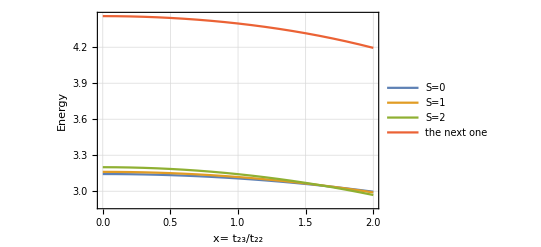

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

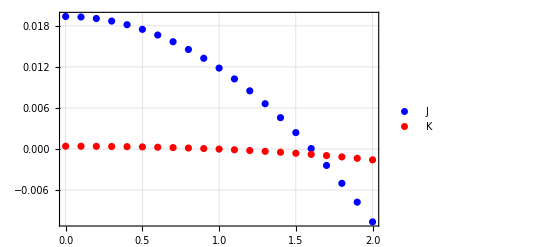

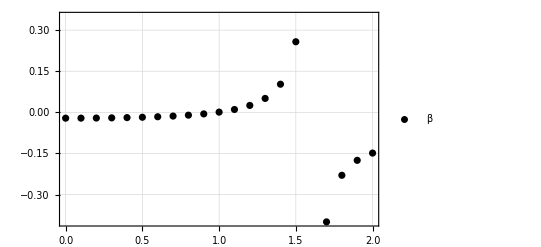

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```